Analytical solution for percolation threshold using renormalization group analysis

For a Forrest fire to spread across a section, it is not sufficient that the trees be placed in an appropriate formation that the fire could spread if they were all on fire, a sufficient set of trees must also be ignited so as to spread the fire. I make the simplifying assumption that all the fire does not spread from left to right in the 2x2block grid, i.e. that one of the two left most blocks must be ignited that before the right-most columns of blocks have a chance to be ignited. Consequently, the probability of the blocks in the right-most column being ignited are the same independent of the the fire status of the left-most column.

This said, let us enumerate all the possible ways this could happen : 

1. There are 4 tree blocks in the 2 x2 block section : 
This case is analogous to the case with i = 1 in Sayama 12.5, only here p = 1 and the conductance probability is instead a function of i :

```mathematica
i^4+ 4 i^3(1-i) + 4 i^2(1-i)^2
```

4 (1-i)^2 i^2+4 (1-i) i^3+i^4

2. There are 3 blocks in the 2x2 block section:
There are four ways to place 3 blocks into a 2x2 block section.
For each, there are 3 possible configurations of ignition that could allow for the fire to propagate across the length scale:
1. All 3 light up
2.  Ignite two such that the fire spreads along the diagonal
3. Ignite two such that the fire spreads horizontally
We can express the probability of each scenario as follows

```mathematica
4(i^3+2 i^2(1-i))
```

4 (2 (1-i) i^2+i^3)

3. There are 2 tree blocks in the 2 x2 block section
For the fire to spread in this scenario, both need to be ignited.
There are four ways to place 2 tree blocks

```mathematica
4(i^2)
```

4 i^2

Weighting by the probability of being in each scenario, and combining all expressions

```mathematica
p^4(i^4+ 4 i^3(1-i) + 4 i^2(1-i)^2) + 4 p^3(1-p)(4(i^3+2 i^2(1-i))) + 4 p^2(1-p)^2(4(i^2)) // FullSimplify
```

i^2 p^2 (16-16 i p+(-12+i (12+i)) p^2)

## Solving for critical thresholds

```mathematica
iterativeMap[i_, p_] := i^2 p^2 (16-16 i p+(-12+i (12+i)) p^2)
```

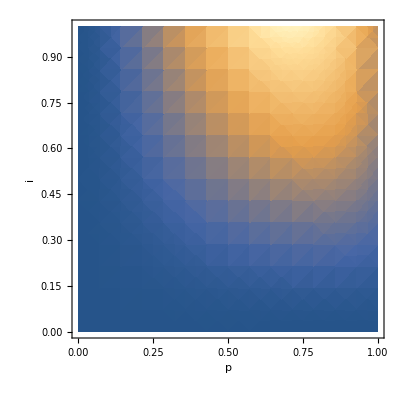

```mathematica
(*Plot iterative map for all values i and p on 0 and 1*)
DensityPlot[iterativeMap[i, p], {p, 0, 1}, {i, 0, 1}, Frame->True, FrameLabel->{p, i}]
```

#### Deriving an expression for the for the critical threshold f(p)=i, beyond which the fire will spread across an undefined length scale.

To solve for the critical values, we want to find the values for which ϕ(i, p) = i, p. Where ϕ(i, p) is the iterative map for length scales.

```mathematica
Solve[iterativeMap[i, p]==i && 0<i<1 && 0<p<1, {i}, Reals] // FullSimplify
```

{{i→ConditionalExpression[Root[-1+(8 p^2+16 p^3-20 p^4) #1+(-16 p^3+12 p^4) #1^2+p^4 #1^3&,1],1/(√7)<p<1]}}

Irrespective of i, there is no chance for the fire to spread if p < 1/(√7).

Visualizing the result for the critical threshold values for {p,i},

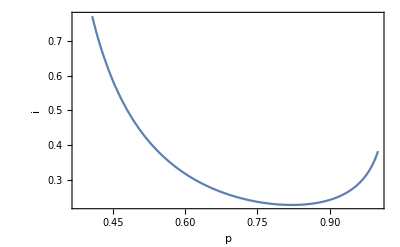

```mathematica
Plot[Root[-1+(8 p^2+16 p^3-20 p^4) #1+(-16 p^3+12 p^4) #1^2+p^4 #1^3&,1], {p, 1/(√7), 1}, Frame->True, FrameLabel->{p, i}]
```

#### In-class work: Doing forrest fire with i=1 and Von Neumann neighbourhood

```mathematica
p^4 + 4(p^3(1-p)) + 2(p^2(1-p)^2) // Simplify
```

-p^2 (-2+p^2)

```mathematica
map[p_] := -p^2 (-2+p^2)
Solve[map[p]==p && 0<p<1, p]4
```

{{p→1/2 (-1+√5)}}

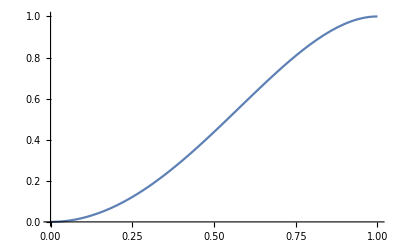

```mathematica
Plot[map[p],{p, 0, 1}]
```